This is based on MWCPlot, originally developed for my presentation in London, but now redisigned (hopefully) to function with sliders as a “Manipulate” object in a CDF.

MWCPlot is quite general; any quantity resulting from the simulation can be plotted against any other resulting quantity. Here I assume that the x-axis will always be PO2, and that users would want to consider how all R, all T, or Y species vary with PO2. 

So here is my list of possible plots:

	0	Y vs. PO2
	1	All R vs. PO2
	2	R0, R1, R2, R3, R4, fR vs. PO2
	3	0 & 2
	4	0 & 1
	5	All T vs. PO2
	6	T0, T1, T2, T3, T4, fT vs PO2
	7	0 & 6
	8	0 & 5
	9	0, 2, 6
	10	0, 1, 5

```mathematica
MWCGenGraph[
arg_, MWCDataSet_
] := Module[
{
YPLOT,
FIVERPLOT,
fRPLOT,
FIVETPLOT,
fTPLOT,
OUTPUT,
iterator
},
YPLOT = ListPlot[
Transpose[
{#[[1]]&/@MWCDataSet,#[[3]]& /@ MWCDataSet}
], 
PlotRange -> {All, {0, 1}},
PlotJoined -> True,
PlotStyle -> {Black, Thickness[0.01]},
ImageSize -> {9 72, 6 72},
Axes -> False,
Frame -> True,
FrameLabel -> {"PO_2, torr", "Y"},
TextStyle-> {FontFamily -> "Arial", FontSize -> 18},
FrameStyle -> Thickness[0.005],
PlotLabel -> "Y vs. PO_2"
];
fRPLOT = ListPlot[
Transpose[
{#[[1]]&/@MWCDataSet,#[[5]]& /@ MWCDataSet}
],
PlotRange -> {All, {0, 1}},
PlotJoined -> True,
PlotStyle -> {Red, Thickness[0.01]}
];
FIVERPLOT = ListPlot[
Table[
Transpose[
{#[[1]]&/@MWCDataSet,#[[iterator]]/(#[[4]]+#[[5]])&/@MWCDataSet}
], 
{iterator, 11, 15}
],
PlotRange -> {All, {0, 1}},
PlotStyle -> {
{Dotted,Red, Thickness[0.01]}, 
{DotDashed,Red, Thickness[0.01]}, 
{Dashing[Small],Red, Thickness[0.01]},
{Dashing[Medium],Red, Thickness[0.01]},
{Dashing[Large],Red, Thickness[0.01]}
},
PlotLegend->{
Text[Style["R_4O_(2_0)",Black,Italic,14]],
Text[Style["R_4O_(2_1)",Black,Italic,14]],
Text[Style["R_4O_(2_2)",Black,Italic,14]],
Text[Style["R_4O_(2_3)",Black,Italic,14]],
Text[Style["R_4O_(2_4)",Black,Italic,14]]
},
PlotMarkers->{MarkerR4O20, MarkerR4O21, MarkerR4O22, MarkerR4O23, MarkerR4O24},
LegendPosition->{.775,-0.35}, 
ImageSize -> {9 72, 6 72},
Axes -> False,
 Frame -> True,
FrameLabel -> {Text[Style["PO_2, torr", Black, 18]],Text[Style["Fraction of Relaxed Species", Black, 18]]} ,
TextStyle-> {FontFamily -> "Arial", FontSize -> 18},
FrameStyle -> Thickness[0.005],
PlotLabel -> Text[Style["Relaxed Species vs. PO_2", Black, 18]]
];
FIVETPLOT = Show[
Table[
ListPlot[
Transpose[
{#[[1]]&/@MWCDataSet,#[[iterator]]/(#[[4]]+#[[5]])&/@MWCDataSet}
],
PlotRange -> {All, {0, 1}}
],
{iterator, 6, 10}
]
];
fTPLOT = ListPlot[
Transpose[
{#[[1]]&/@MWCDataSet,#[[4]]& /@ MWCDataSet}
],
PlotRange -> {All, {0, 1}}
];
OUTPUT = Which[
arg == 0, YPLOT,
arg == 1, fRPLOT,
arg == 2, Show[
FIVERPLOT,fRPLOT],
arg == 3, Show[
YPLOT, FIVERPLOT],
arg ==4, Show[
YPLOT, fRPLOT],
arg == 5, fTPLOT,
arg == 6, Show[
FIVETPLOT, fTPLOT
],
arg == 7, Show[
YPLOT, FIVETPLOT
],
arg == 8, Show[
YPLOT, fTPLOT
],
arg == 9, Show[
YPLOT, FIVERPLOT, FIVETPLOT
],
arg == 10, Show[
YPLOT, fRPLOT, fTPLOT
]
]
]
```

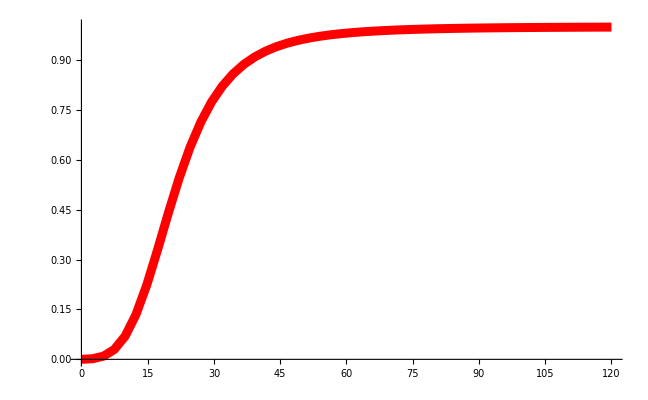

```mathematica
test1 = MWCGenGraph[
1, mwcsolutionset
]
```

```mathematica
?Needs
```

RowBox[{"Needs", "[", StyleBox["\"\!\(\*StyleBox[\"context\",\"TI\"]\)`\"", ShowStringCharacters->True], "]"}] loads an appropriate file if the specified context is not already in $Packages. 
RowBox[{"Needs", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"context\",\"TI\"]\)`\"", ShowStringCharacters->True], ",", StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\)\"", ShowStringCharacters->True]}], "]"}] loads StyleBox["file", "TI"] if the specified context is not already in $Packages.